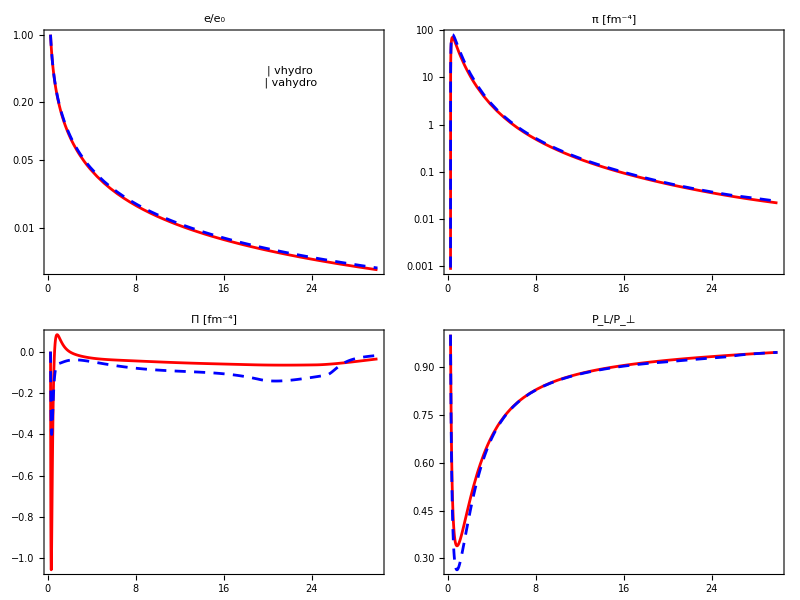

```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[];

stylesVH={Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],
Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]]};

stylesVAH={Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[1,0,0],AbsoluteThickness[2]],
Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[1,0,0],AbsoluteThickness[2]]};

EnergyDensityDataRawVH=Import[wd<>"/eplot_vh.dat"];
piDataRawVH=Import[wd<>"/piplot_vh.dat"];
PiDataRawVH=Import[wd<>"/bulkplot_vh.dat"];
plptDataRawVH=Import[wd<>"/plptplot_vh.dat"];

EnergyDensityDataVH= Take[EnergyDensityDataRawVH,{2,Length[EnergyDensityDataRawVH]}];
piDataVH= Take[piDataRawVH,{2,Length[piDataRawVH]}];
PiDataVH= Take[PiDataRawVH,{2,Length[PiDataRawVH]}];
plptDataVH= Take[plptDataRawVH,{2,Length[plptDataRawVH]}];

t0 = EnergyDensityDataVH[[1,1]];
tf = EnergyDensityDataVH[[Length[EnergyDensityDataVH],1]];

energydensityVH = Interpolation[EnergyDensityDataVH[[All,{1,2}]]];
piVH = Interpolation[piDataVH[[All,{1,2}]]];
bulkVH = Interpolation[PiDataVH[[All,{1,2}]]];
plptVH = Interpolation[plptDataVH[[All,{1,2}]]];


EnergyDensityDataRawVAH=Import[wd<>"/eplot_vah.dat"];
piDataRawVAH=Import[wd<>"/piplot_vah.dat"];
PiDataRawVAH=Import[wd<>"/bulkplot_vah.dat"];
plptDataRawVAH=Import[wd<>"/plptplot_vah.dat"];

EnergyDensityDataVAH= Take[EnergyDensityDataRawVAH,{2,Length[EnergyDensityDataRawVAH]}];
piDataVAH= Take[piDataRawVAH,{2,Length[piDataRawVAH]}];
PiDataVAH= Take[PiDataRawVAH,{2,Length[PiDataRawVAH]}];
plptDataVAH= Take[plptDataRawVAH,{2,Length[plptDataRawVAH]}];

t0 = EnergyDensityDataVH[[1,1]];
tf = EnergyDensityDataVH[[Length[EnergyDensityDataVH],1]];

energydensityVH = Interpolation[EnergyDensityDataVH[[All,{1,2}]]];
piVH = Interpolation[piDataVH[[All,{1,2}]]];
bulkVH = Interpolation[PiDataVH[[All,{1,2}]]];
plptVH = Interpolation[plptDataVH[[All,{1,2}]]];

energydensityVAH = Interpolation[EnergyDensityDataVAH[[All,{1,2}]]];
piVAH = Interpolation[piDataVAH[[All,{1,2}]]];
bulkVAH = Interpolation[PiDataVAH[[All,{1,2}]]];
plptVAH = Interpolation[plptDataVAH[[All,{1,2}]]];

legend1=Panel[Grid[{{Graphics[{stylesVH[[1]],Line[{{0,0},{1,0}}]},ImageSize->28,AspectRatio->0.2],Style["vhydro",FontSize->12,FontFamily->"Times"]},
{Graphics[{stylesVAH[[1]],Line[{{0,0},{1,0}}]},ImageSize->28,AspectRatio->0.2],Style["vahydro",FontSize->12,FontFamily->"Times"]}}],Background->White];

energyplot=LogPlot[{energydensityVAH[t],energydensityVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVAH[[1]],stylesVH[[1]]},PlotLabel->Style["e/e_0",FontSize->16,FontFamily->"Times"],ImageSize->250,Frame->True,Axes->False,BaseStyle->{FontSize->14},AspectRatio->0.75,Epilog->Inset[legend1,{22,-1}]];
bulkplot = Plot[{bulkVAH[t],bulkVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVAH[[3]],stylesVH[[3]]},ImageSize->250,PlotLabel->Style["Π [fm^-4]",FontSize->16,FontFamily->"Times"],Frame->True,Axes->False,FrameLabel->{"τ (fm/c)"},BaseStyle->{FontSize->14},AspectRatio->0.75];
piplot = LogPlot[{piVAH[t],piVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVAH[[2]],stylesVH[[2]]},ImageSize->250,PlotLabel->Style["π [fm^-4]",FontSize->16,FontFamily->"Times"],Frame->True,Axes->False,BaseStyle->{FontSize->14},AspectRatio->0.75];
plptplot = Plot[{plptVAH[t],plptVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVAH[[4]],stylesVH[[4]]},ImageSize->250,PlotLabel->Style["P_L/P_⊥",FontSize->16,FontFamily->"Times"],Frame->True,Axes->False,FrameLabel->{"τ (fm/c)"},BaseStyle->{FontSize->14},AspectRatio->0.75];

a1=Grid[{{energyplot,piplot},{bulkplot,plptplot}}]

Export["compare_hydro.pdf",a1];
```

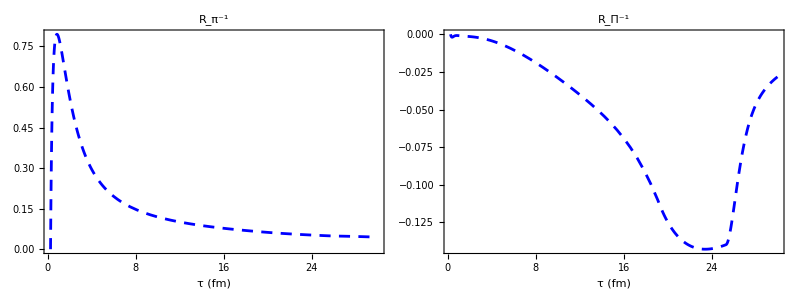

```mathematica
RpiInverseDataRawVH=Import[wd<>"/RpiInvplot_vh.dat"];
RbulkInverseDataRawVH=Import[wd<>"/RbulkInvplot_vh.dat"];

RpiInverseDataVH= Take[RpiInverseDataRawVH,{2,Length[RpiInverseDataRawVH]}];
RbulkInverseDataVH= Take[RbulkInverseDataRawVH,{2,Length[RbulkInverseDataRawVH]}];

RpiInverseVH = Interpolation[RpiInverseDataVH[[All,{1,2}]]];
RbulkInverseVH = Interpolation[RbulkInverseDataVH[[All,{1,2}]]];


Grid[{{Plot[{RpiInverseVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->stylesVH[[1]],ImageSize->320,Frame->True,Axes->False,PlotLabel->Style["R_π^-1",FontSize->16,FontFamily->"Times"],FrameLabel->{"τ (fm)",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
Plot[{RbulkInverseVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->stylesVH[[3]],ImageSize->320,Frame->True,Axes->False,PlotLabel->Style["R_Π^-1",FontSize->16,FontFamily->"Times"],FrameLabel->{"τ (fm)",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]
```